### Categorization

Tutorial

VQM

VQM`

VQM/tutorial/ComplexPlot

### Keywords

Details

# ComplexPlot

### Abstract

This package provides commands for visualizing complex-valued functions by generating two-dimensional ColorDensityGraphics, ContourGraphics and three dimensional SurfaceGraphics of complex-valued functions with a color code for complex numbers. These packages are distributed with the book Advanced Visual Quantum Mechanics, Springer-Verlag New York, 2004.

Additional visualization functions

QComplexDensityPlot[f[x,y],{x,xmin,xmax},{y,ymin,ymax}] | generate a two dimensional ColorDensityGraphics of a complex-valued function f of two variables x and y. Similar to DensityPlot.
QComplexContourPlot[f[x,y],{x,xmin,xmax},{y,ymin,ymax}] | combines a ComplexDensityPlot of a function f with a ContourPlot of Abs[f].
QComplexPlot3D[f[x,y],{x,xmin,xmax},{y,ymin,ymax}] | generates a two dimensional SurfaceGraphics of a complex-valued function f.

Visualizing complex functions.

This loads the package.

### This loads the package.

```mathematica
Needs["VQM`"]
```

The main package automatically loads the package VQM`ComplexPlot` and VQM`ColorMaps`.

```mathematica
QComplexDensityPlot[x + I y, {x,-4,4}, {y,-4,4}]
```

-Graphics-

This graphic illustrates the default color map of the complex numbers, which is used in this package. This color map is defined in the HLS color system as follows. Hue = Arg[z]/2/Pi, Lightness = (2/Pi) ArcTan[r/R], Saturation = 1. This color map can be understood as a stereographic mapping from the complex plane to the surface of a sphere of radius R composed with a continuous mapping from the sphere onto the surface of the color manifold.
Note that zeros of a complex function appear black, real values are red, poles are white. At the zeros and at poles, the phase is not defined, hence an error message Arg::indet will appear

The plot can be regenerated using any option that can be given for the DensityPlot function. This turns off the mesh and displays axes.

```mathematica
QComplexDensityPlot[x+I y,{x,-4,4},{y,-4,4},Mesh->None,Axes->True]
```

-Graphics-

The following combines a QComplexDensityPlot of Sin[z] with a ContourPlot of Sin[x]Cos[y].

```mathematica
gr1=QComplexDensityPlot[Sin[x+ⅈ y],{x,-π,π},{y,-π,π},Mesh->False];
gr2=ContourPlot[Sin[x] Cos[y],{x,-π,π},{y,-π,π},ContourShading->False,Exclusions->{Abs[y]==π/2,x*y==0}];
Show[gr1,gr2]
```

-Graphics-

This combines a ComplexDensityPlot of f[z] with a ContourPlot of the absolute value Abs[f[z]]. The mesh and the shading of contours are turned off automatically.

```mathematica
QComplexContourPlot[Cos[x + I y],
{x,-Pi,Pi},{y,-1.5,1.5},Contours->10]
```

-Graphics-

This gives a surface plot of f[z] = Sin[z].

```mathematica
QComplexPlot3D[Sin[x + I y],{x,-Pi,Pi},{y,-1,2}]
```

-Graphics3D-

There are list-plot versions of the commands introduced above.

QListComplexDensityPlot[array] | generate a two dimensional ColorDensityGraphics of a  two dimensional array of com
QListComplexContourPlot[array] | combines a ComplexDensityPlot of an array with a ContourPlot of Abs[array].
ListComplexPlot3D | generates a two dimensional SurfaceGraphics of a two dimensional array of complex numbers.

List-plot versions.

The array has to be of the form {{z_11,z_12,...,z_(1n)},...,{z_m1,z_m2,...,z_mn}}, where the z_ij are complex numbers.

This generates a two-dimensional table of complex values.

```mathematica
A=Table[BesselJ[0,x + I y] + I BesselY[0,x + I y],{y,-1.5,1.5,.125},{x,-3.,1.,.1}];
```

Display the table with ListComplexDensityPlot. We use options for fine-tuning the visualization.

```mathematica
QListComplexDensityPlot[A,Mesh->False,DataRange->{{-3,1},{-1.5,1.5}},AspectRatio->3/4]
```

-Graphics-

The graphic above shows  the Hankel function J_0 + i Y_0. We see the approximate positions of a zero in the lower half plane, the pole at the origin, and the branch cut along the negative real axis.

The commands ColorDensityPlot and ListColorDensityPlot generate a Graphics object.

```mathematica
gr1= QComplexDensityPlot[3(x+I y)^2 Exp[-(x^2+y^2)],{x,-2,2},{y,-2,2}]
```

-Graphics-

```mathematica
QComplexPlot3D[3(x+I y)^2 Exp[-(x^2+y^2)],{x,-2,2},{y,-2,2},ImageSize->360,Background->Black]
```

-Graphics3D-

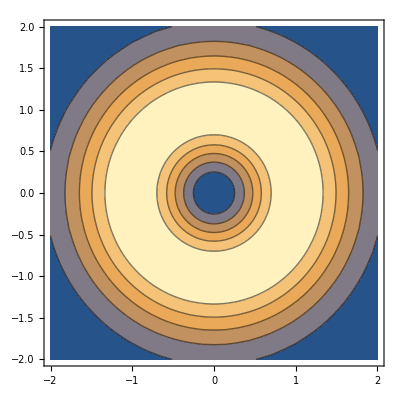

```mathematica
QComplexContourPlot[3(x+I y)^2 Exp[-(x^2+y^2)],{x,-2,2},{y,-2,2},Contours->5,QComplexToColorMap->(GrayLevel[#1]&),ContourShading->True]
```

```mathematica
QComplexContourPlot[3(x+I y)^2 Exp[-(x^2+y^2)],{x,-2,2},{y,-2,2},Contours->5,QComplexToColorMap->None,ContourShading->{Red,Blue,Green},ContourStyle->Opacity[0.4]]
```

-Graphics-

```mathematica
Options[QComplexContourPlot,Antialiasing]
```

{Antialiasing→True}

The built-in colormap can be modified by several options.

option name | default value | 
QSphereRadius | 1 | The radius of the sphere used for the stereographic projection
QValueRange | {0,1} | The range of absolute values which are to be colored
QLightnessRange | {0,1} | Defines the minimal and maximal lightness of the colors
QComplexToColorMap | $QComplexToColorMap | Use a different color map

Options for the color map.

The options QSphereRadius, QValueRange, and QLightnessRange influence the built-in color map. Use large (resp. small) values of QSphereRadius if you want to investigate a complex function in a region where its absolute values are large (resp. small). SphereRadius->R causes all complex values with absolute value R to be drawn at maximal brightness and saturation. ValueRange->{rmin,rmax} causes all f[z] with Abs[f[z]]<rmin to be drawn with minimal lightness (usually black); all f[z] with Abs[f[z]]>rmax are drawn at maximal lightness (usually white). The settings for maximal and minimal lightness are controlled by the option LightnessRange. The built-in color map is $ComplexToColorMap. It can be replaced by a different color map by setting the option ComplexToColorMap.

QComplexToColor[z] | associate a color directive to a complex number z according to the option ComplexToColorMap.

QComplexToColor.

The function QComplexToColor is actually defined in the package VQM`ColorMaps`, which is loaded automatically by VQM`ComplexPlot`.

Maximal and minimal lightness is set to 1/2. Thus only the phases are mapped to a color, the information on the absolute value is lost.

```mathematica
QComplexDensityPlot[ x + I y, {x,-4,4},{y,-4,4},QLightnessRange->{.5,.5}]
```

-Graphics-

Here the ValueRange is set to {1,4}.

```mathematica
QComplexDensityPlot[ x + I y, {x,-4,4},{y,-4,4},QValueRange->{1,4}]
```

-Graphics-

In ValueRange->{v1,v2} the value v1 may be larger than v2. Plotting f with ValueRange->{Infinity,0} is the same as plotting 1/Conjugate[f] with the default settings:

```mathematica
QComplexDensityPlot[ x + I y, {x,-4,4},{y,-4,4},QValueRange->{Infinity,0}]
```

-Graphics-

A color map receives information about absolute value and phase of a complex function f. Here is an example

```mathematica
mymap[r_,phi_]:=
Hue[r,Mod[phi/2/Pi,1],Mod[phi/Pi,1]]
```

```mathematica
QComplexDensityPlot[x+I y,{x,-1,1},{y,-1,1},QComplexToColorMap->mymap]
```

-Graphics-

QColorArrayPlot[array] | generates a raster image of an array of color directives.

QColorArrayPlot.

Define a two dimensional array of colors.

```mathematica
colortable=Table[RGBColor[Mod[x,1],Mod[y,1],Mod[x-y,1]],{y,0,1,.1},{x,0,1,.1}];
```

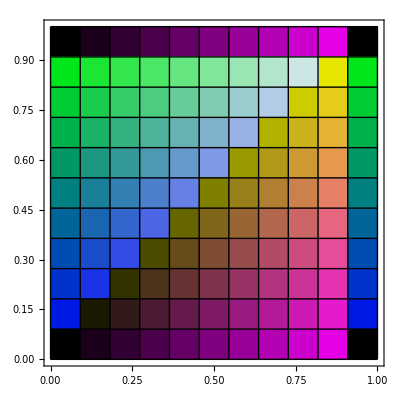

```mathematica
QColorArrayPlot[colortable,DataRange->{{0,1},{0,1}}]
```

This command can be used to display color images in Mathematica.

More About

Related Tutorials

Related Wolfram Education Group Courses